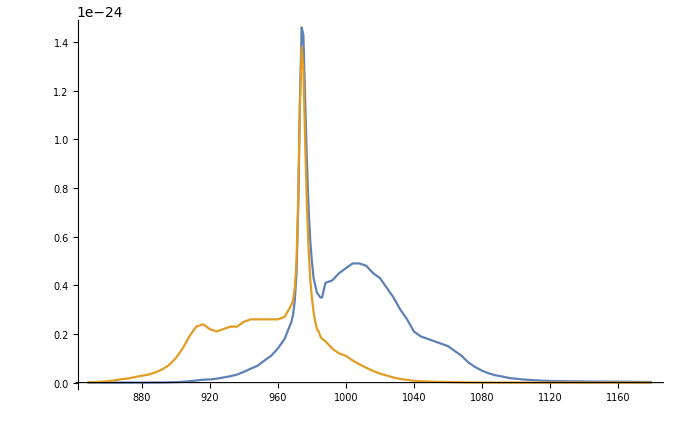

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]]];
σa=Interpolation[σ[[All,{1,3}]]];
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λp=960;(*нм*)
λs=1064;(*нм*)
Ps=(Aeff h c)/(λs 10^-19);
Pp=Aeff h c/(λp 10^-9);

L=2;

σp12=σa[λp];
σp21=σe[λp];
σs12=σa[λs];
σs21=σe[λs];
```

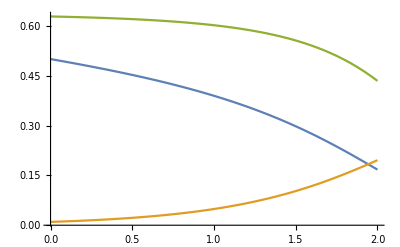

```mathematica
(*Усилитель*)
sol=NDSolve[{
0==ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN, 
Pp ρp[0]==0.5,Ps ρs[0]==10 10^-3
},{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->Infinity];

Plot[Evaluate[{Pp ρp[z],Ps ρs[z],N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```

Домашнее задание 
1) Изучить Consistent Initialization, AccuracyGoal, PrecisionGoal, tutorial/NDSolveBVP
2) Уметь вывести формулу инверсии просветления среды. Построить график зависимости инверсии просветления иттербия от длины волны.
3) Рассмотреть усилитель, где изменением всех искомых величин по z можно пренебречь, считать инверсию постоянной и заданной по всей длине x%. Аналитически решить эту задачу в Mathematica. Построить график спектра усиления такого иттербиевого волоконного усилителя. Необходимые константы и параметры задачи взять из семинара.
4) Слабый сигнал - такой сигнал на входе в усилитель, влиянием которого на инверсию в усилителе можно пренебречь. Исходя из этой посылки упростить скоростные уравнения и построить график спектра коэффициента усиления слабого сигнала для усилителя, описанного в семинарской задаче. Изучить понятие мощности насыщения.